# Лабораторная работа No.2

```mathematica
Чобану Артём I1902
```

### Описание функций

### 1. Map (также используется как “/@”)

Mappaclet:ref/Map[f,expr]orf/@expr 
Устанавливает соответствие f с каждым элементом выражения.

Mappaclet:ref/Map[f,expr,levelspec]
Устанавливает соответствие f с выражением указанного уровня.

Mappaclet:ref/Map[f]
Представляет собой оператор Map,paclet:ref/Mapкоторый можно использовать с выражением f.

### Примеры

```mathematica
Map[f,{a,b,c,d,e}]
```

{f[a],f[b],f[c],f[d],f[e]}

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

```mathematica
(1+g[#])&/@{a,b,c,d,e}
```

{1+g[a],1+g[b],1+g[c],1+g[d],1+g[e]}

```mathematica
Function[x,x^2]/@{1,2,3,4}
```

{1,4,9,16}

```mathematica
Map[f,{{a,b},{c,d,e}}]
```

{f[{a,b}],f[{c,d,e}]}

```mathematica
Map[f,{{a,b},{c,d,e}},{2}]
```

{{f[a],f[b]},{f[c],f[d],f[e]}}

```mathematica
Map[f,{{a,b},{c,d,e}},2]
```

{f[{f[a],f[b]}],f[{f[c],f[d],f[e]}]}

```mathematica
Map[f][{a,b,c,d}]
```

{f[a],f[b],f[c],f[d]}

```mathematica
Map[h,<|a->b, c->d|>]
```

<|a→h[b],c→h[d]|>

### 2. Apply (@@)

f@@exprorApplypaclet:ref/Apply[f,expr]
Подставляет выражение в голову функции(заменяет голову выражения функцией f)

f@@@exprorApplypaclet:ref/Apply[f,expr,{1}]
Заменяет несколько голов выражения 1 уровня.

Applypaclet:ref/Apply[f,expr,levelspec]
Заменяет головы части выражения указанного уровня.

Applypaclet:ref/Apply[f]
Операторная формаApplypaclet:ref/Apply,применяемая к любому выражению.

### Примеры

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
Plus@@{a,b,c,d}
```

a+b+c+d

```mathematica
f@@{{a,b},{c},d}
```

f[{a,b},{c},d]

```mathematica
Apply[f][{{a,b},{c},d}]
```

f[{a,b},{c},d]

```mathematica
Apply[f,<|1->a,2->b,3->c|>]
```

f[a,b,c]

```mathematica
Apply[f,<|1->a,2->b,3->c,4->{d,{e}}|>,{2}]
```

<|1→a,2→b,3→c,4→{d,f[e]}|>

```mathematica
Apply[f,<|1->a,2->b,3->c,4->{d,{e}}|>,{0,2}]
```

f[a,b,c,f[d,f[e]]]

### 3. Nest

```mathematica
Nestpaclet:ref/Nest[f,expr,n]
Возвращает выражение f, которое применили n раз к выражению.
```

### 3.1 NestList

```mathematica
NestListpaclet:ref/NestList[f,expr,n]
Вощвращает список результатов применения выражения f к выражению n раз.
```

### 3.2 NestWhileList

```mathematica
NestWhileListpaclet:ref/NestWhileList[f,expr,test]
Возвращает список результатов применения f к выражению до тех пор пока test перестанет возвращать Truepaclet:ref/True.
```

```mathematica
NestWhileListpaclet:ref/NestWhileList[f,expr,test,m]
Подставляет последние m результатов для test в качестве аргументов.
```

```mathematica
NestWhileListpaclet:ref/NestWhileList[f,expr,test,Allpaclet:ref/All]
Подставляет все результаты в test в качестве аргументов
```

```mathematica
NestWhileListpaclet:ref/NestWhileList[f,expr,test,m,max]
applies f at most max times.
```

### 3.3 NestWhile

```mathematica
NestWhilepaclet:ref/NestWhile[f,expr,test]
starts with expr, then repeatedly applies f until applying test to the result no longer yields Truepaclet:ref/True.
```

```mathematica
NestWhilepaclet:ref/NestWhile[f,expr,test,m]
supplies the most recent m results as arguments for test at each step.
```

```mathematica
NestWhilepaclet:ref/NestWhile[f,expr,test,Allpaclet:ref/All]
supplies all results so far as arguments for test at each step.
```

```mathematica
NestWhilepaclet:ref/NestWhile[f,expr,test,m,max]
applies f at most max times.
```

```mathematica
NestWhilepaclet:ref/NestWhile[f,expr,test,m,max,n]
applies f an extra n times.
```

```mathematica
NestWhilepaclet:ref/NestWhile[f,expr,test,m,max,-n]
returns the result found when f had been applied n fewer times.
```

### 3.4 NestGraph

```mathematica
NestGraphpaclet:ref/NestGraph[f,expr,n]
Возвращает граф, полученный стартуя с выражения, и применяя f рекурсивно n раз.
```

```mathematica
NestGraphpaclet:ref/NestGraph[f,{Subscript[expr, 1],Subscript[expr, 2],…},n]
Возвращает граф, аолученный применяя f к Subscript[expr, 1], Subscript[expr, 2], ….
```

```mathematica
NestGraphpaclet:ref/NestGraph[f,graph,n]
Возвращает граф, полученный применяя f к вершинам графа graph.
```

### Примеры

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
NestWhileList[Log,100,#>0&]
```

{100,Log[100],Log[Log[100]],Log[Log[Log[100]]],Log[Log[Log[Log[100]]]]}

```mathematica
NestWhile[Log,100,#>0&]
```

Log[Log[Log[Log[100]]]]

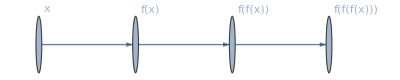

```mathematica
NestGraph[f,x,3,VertexLabels->"Name",ImagePadding-> 40]
```

### 4. Fold

```mathematica
Foldpaclet:ref/Fold[f,x,list]
Возвращает последний элемент FoldListpaclet:ref/FoldList[f,x,list].
```

```mathematica
Foldpaclet:ref/Fold[f,list]
Эквивалентен Foldpaclet:ref/Fold[f,Firstpaclet:ref/First[list],Restpaclet:ref/Rest[list]].
```

```mathematica
Foldpaclet:ref/Fold[f]
Операторная форма Foldpaclet:ref/Fold.
```

### 4.1 FoldList

```mathematica
FoldListpaclet:ref/FoldList[f,x,{a,b,…}]
Возвращает {x,f[x,a],f[f[x,a],b],…}.
```

```mathematica
FoldListpaclet:ref/FoldList[f,{a,b,c,…}]
Возвращает {a,f[a,b],f[f[a,b],c],…}.
```

```mathematica
FoldListpaclet:ref/FoldList[f]
Операторная форма FoldListpaclet:ref/FoldList.
```

### 4.2 FoldPair

```mathematica
FoldPairpaclet:ref/FoldPair[f,Subscript[y, 0],list] 
Возвращает последний элемент FoldPairListpaclet:ref/FoldPairList[f,Subscript[y, 0],list].
```

```mathematica
FoldPairpaclet:ref/FoldPair[f,Subscript[y, 0],list,g]
возвращает последний элемент FoldPairListpaclet:ref/FoldPairList[f,Subscript[y, 0],list,g].
```

```mathematica
FoldPairpaclet:ref/FoldPair[f,{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],…}]
Эквивалентен FoldPairpaclet:ref/FoldPair[f,Subscript[a, 0],{Subscript[a, 1],Subscript[a, 2],…}].
```

### 4.3 FoldPairList

```mathematica
FoldPairListpaclet:ref/FoldPairList[f,Subscript[y, 0],{Subscript[a, 1],Subscript[a, 2],…}]
gives the list of successive Subscript[x, i] obtained by applying f to pairs of the form {Subscript[y, i-1],Subscript[a, i]}, where at each step f returns {Subscript[x, i],Subscript[y, i]}.
```

```mathematica
FoldPairListpaclet:ref/FoldPairList[f,Subscript[y, 0],list,g]
gives the list of successive values of g[{Subscript[x, i],Subscript[y, i]}].
```

```mathematica
FoldPairListpaclet:ref/FoldPairList[f,{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],…}]
Эквивалентен FoldPairListpaclet:ref/FoldPairList[f,Subscript[a, 0],{Subscript[a, 1],Subscript[a, 2],…}].
```

### Примеры

```mathematica
Fold[List,x,{a,b,c,d}]
```

{{{{x,a},b},c},d}

```mathematica
FoldList[Plus,0,{a,b,c,d}]
```

{0,a,a+b,a+b+c,a+b+c+d}

```mathematica
FoldPair[{p[#1,#2],q[#1,#2]}&,u,{1,2,3}]
```

p[q[q[u,1],2],3]

```mathematica
FoldPairList[{p[#1,#2],q[#1,#2]}&,u,{1,2,3,4}]
```

{p[u,1],p[q[u,1],2],p[q[q[u,1],2],3],p[q[q[q[u,1],2],3],4]}

## Задачи из 25 главы

25.1 Use /@ and Range to reproduce the result of Table[f[n], {n, 5}].

```mathematica
Table[f[n], {n, 5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Ответ:
```

```mathematica
f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

25.2 Use /@ twice to generate Table[f[g[n]], {n, 10}].

```mathematica
Table[f[g[n]], {n, 10}]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
Ответ:
```

```mathematica
f/@g/@Range[10]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

25.3 Use // to create a[b[c[d[x]]]].

```mathematica
Ответ:
```

```mathematica
x//d//c//b//a
```

a[b[c[d[x]]]]

25.4 Make a list of letters of the alphabet, with a frame around each one.

```mathematica
Ответ:
```

```mathematica
Framed/@Alphabet["Russian"]
```

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

```mathematica
Второй вариант решения:
```

```mathematica
Map[Framed,Alphabet["Russian"]]
```

Или:{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

25.5 Color negate an image of each planet, giving a list of the results.

```mathematica
Планета Земля:
```

```mathematica
ColorNegate[EntityValue[Entity["Planet", "Earth"], "Image"]]
```

-Graphics-

```mathematica
Список всех планет:
```

```mathematica
EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
ColorNegate /@ EntityValue[EntityList["Planet"], "Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

25.6 Use /@ to draw separate maps of each country in the G5.

```mathematica
GeoListPlot/@EntityList@CountryData["G5"]
```

GeoGraphics::tiles: Unable to download 2 tiles of the geo background image.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

25.7 Binarize each flag in Europe, and make an image collage of the result.

```mathematica
Binarize /@EntityValue[Entity["GeographicRegion", "Europe"]["Countries"], "Flag"]//ImageCollage
```

-Graphics-

25.8 Find a list of the dominant colors in images of the planets, putting the results for each planet in a column.

```mathematica
Column /@DominantColors/@ EntityValue[EntityList["Planet"], "Image"]
```

{GrayLevel[0.00011229906593901449]
GrayLevel[0.3980514107663027]
GrayLevel[0.601813674014136],RGBColor[0.8853264306826334, 0.6847268529949845, 0.42566949894088035]
RGBColor[0.0006421200935399591, 0.001403787050459702, 0.0007411313848288354],RGBColor[0.0024607308761682998, 0.002409825849909765, 0.003967421206090782]
RGBColor[0.38129654247557254, 0.407417603373293, 0.4878048510301544]
RGBColor[0.7093694254815353, 0.7271473853772968, 0.8067994700600088]
RGBColor[0.9790087601458787, 0.9820957420547148, 0.9938832755302741]
RGBColor[0.6354967266058315, 0.5479927007559342, 0.5436082783376446],RGBColor[0.0012177592604074837, 0.0015444881616280858, 0.0022826746843563643]
RGBColor[0.5556977647072077, 0.45312590385217083, 0.33304485544842805]
RGBColor[0.9766151688325614, 0.6747992648318544, 0.36945325770650084]
RGBColor[0.24798502535413103, 0.2813950241702763, 0.268991827797094]
RGBColor[0.4966216573650432, 0.5143293528118136, 0.5023891001741378]
RGBColor[0.6400483910016584, 0.7400320950754417, 0.8829317387538683],RGBColor[0.0007307981976981361, 0.0007455534728825817, 0.001656268603959462]
RGBColor[0.6782700167796698, 0.6320723389802164, 0.5998383401396097]
RGBColor[0.8542685312261863, 0.708029391267306, 0.5495181246329811]
RGBColor[0.5603509716497237, 0.44637870186411926, 0.35981723146406597],RGBColor[0.0008760247899435419, 0.0006168176360501591, 0.0013661046503717301]
RGBColor[0.36454996934783984, 0.34744037878046385, 0.3008576081571528]
RGBColor[0.692517109041475, 0.6087663076639458, 0.4578028211778951]
RGBColor[0.9020001346998763, 0.7638458607077833, 0.4927248003003441],RGBColor[0.5487852851004632, 0.6154743166519315, 0.6457812179949426]
RGBColor[0.00262521981356804, 0.002077287070119254, 0.0024668238045117514]
RGBColor[0.22748331195200477, 0.2460562984128471, 0.2551858078977508],RGBColor[0.23776013651293848, 0.3679770485240516, 0.5706310373954431]
RGBColor[0.0007110434985746415, 0.0009022619988835094, 0.0018019970589028553]
RGBColor[0.5017439131644366, 0.5645924759572478, 0.6422977753140859]}

25.9 Find the total of the letter numbers given by LetterNumber for the letters in the word "wolfram".

```mathematica
Total[LetterNumber/@Characters@"wolfram"]
```

88

## Задачи из главы 27

27.1 Make a list of the results of nesting Blur up to 10 times, starting with a rasterized size-30 "X".

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

27.2 Start with x, then make a list by nestedly applying Framed up to 10 times, using a random background color each time.

```mathematica
NestList[Framed[#, Background->RandomColor[]] &, x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

27.3 Start with a size-50 "A", then make a list of nestedly applying a frame and a random rotation 5 times.

```mathematica
NestList[Rotate[Framed[#],RandomReal[{0,360 °}]]&,Style["A",50],5]
```

{A,A,A,A,A,A}

27.4 Make a line plot of 100 iterations of the logistic map iteration 4 #(1-#)&, starting from 0.2

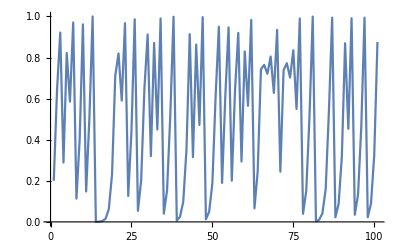

```mathematica
ListLinePlot[NestList[4#(1-#)&, 0.2, 100]]
```

27.5 Find the numerical value of the result from 30 iterations of 1+1/#& starting from 1.

```mathematica
Nest[1+1/#&, 1, 30]//N
```

1.61803

27.6 Create a list of the first 10 powers of 3 (starting at 0) by nested multiplication.

```mathematica
NestList[#*3&, 1, 10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

27.7 Make a list of the result of nesting the (Newton's method) function (#+2/#)/2& up to 5 times starting from 1.0, and then subtract sqrt(2) from all the results.

```mathematica
Substract[ NestList[#+2/2#&, 1 ,5],Sqrt[2]]
```

Substract[{1,2,4,8,16,32},√2]

27.8 Make graphics of a 1000-step 2D random walk which starts at {0, 0}, and in which at each step a pair of random numbers between −1 and +1 are added to the coordinates.

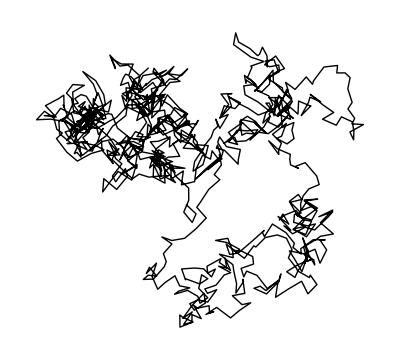

```mathematica
Graphics[Line[NestList[#+RandomReal[{-1,1},2]&, {0,0}, 1000]]]
```

27.9 Make an array plot of 50 steps of Pascal's triangle modulo 2 by starting from {1} and nestedly joining {0} at the beginning and at the end, and adding these results together modulo 2.

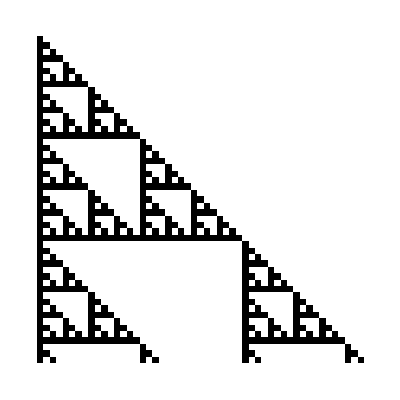

```mathematica
ArrayPlot[NestList[Mod[Join[{0}, #] +Join[#, {0}], 2]&,{1}, 50]]
```

27.10 Generate a graph by starting from 0, then nestedly 10 times connecting each node with value n to ones with values n+1 and 2n.

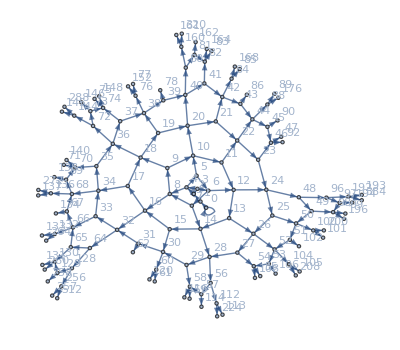

```mathematica
NestGraph[{#+1, 2#}&, 0, 10, VertexLabels->All]
```

27.11 Generate a graph obtained by nestedly finding bordering countries starting from the United States, and going 4 iterations.

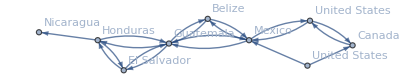

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country", "USA"], 4, VertexLabels->All]
```

27.1 Make a line plot of 100 iterations of linear congruential function Mod[59#, 101]&, starting from 1.

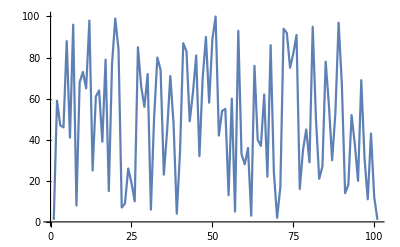

```mathematica
ListLinePlot[NestList[Mod[59#,101]&, 1, 100]]
```

27.2 Create a list of 5 power towers of 2, i.e. 2^2^2...^2 n times, with n from 0 to 4.

```mathematica
NestList[2^#&,1, 4]
```

{1,2,4,16,65536}

27.3 Create a list of 20 power towers of 1.2, i.e. 1.2^1.2^...^1.2 n times, with n from 0 to 19.

```mathematica
NestList[1.2^#&,1, 19]
```

{1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773}

27.4 Generate a list of the numerical values obtained by up to 10 nestings of the function Sqrt[1+#]&

```mathematica
NestList[Sqrt[1+#]&, 1, 10]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

27.5 Make graphics of a 1000-step 3D random walk which starts at {0, 0, 0}, and in which at each step a triple of random numbers between −1 and +1 are added to the coordinates.

```mathematica
Graphics3D[Line[NestList[# + RandomReal[{-1,1},3]&, {0,0,0},1000]]]
```

-Graphics3D-

## Задачи из главы 29

29.1 Use Prime and Array to generate a list of the first 100 primes.

```mathematica
Array[Prime, 100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

29.2 Use Prime and Array to find successive differences between the first 100 primes.

```mathematica
Array[Prime[# + 1] - Prime[#]&, 99]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

29.3 Use Array and Grid to make a 10 by 10 addition table.

```mathematica
Array[#1 + #2&, {10, 10}]//Grid
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

29.4 Use FoldList, Times and Range to successively multiply numbers up to 10 (making factorials).

```mathematica
FoldList[Times,Range[10]]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

29.5 Use FoldList and Array to compute the successive products of the first 10 primes.

```mathematica
FoldList[Times, 1, Array[Prime, 10]]
```

{1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

29.6 Use FoldList to successively ImageAdd regular polygons with between 3 and 8 sides, and with opacity 0.2.

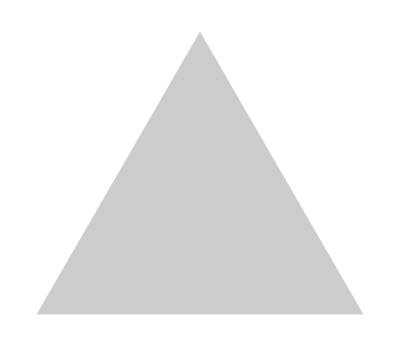
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FoldList[ImageAdd, Table[Graphics[Style[RegularPolygon[n], Opacity[0.2]]], {n, 3, 8}]]
```

+29.1 Use Array to make a 10 by 10 grid where the leading diagonal and everything below it is 1 and the rest is 0.

```mathematica
Array[If[#1≥#2,1,0]&,{10,10}]//Grid
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1